```mathematica
Needs["MaTeX`"]
```

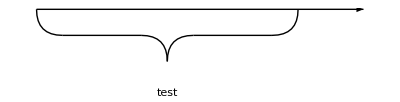

```mathematica
hbrace[p1_,p2_,h_,label_]:=Module[{m,c1,c2,c3,c4,t1,t2,t4},
m=1/2(p1+p2)+{0,h};
c1=p1+1/2{Abs[h],h};
t1=p1+1/2{0,h};
c2=m+1/2{-Abs[h],-h};
t2=m+1/2{0,-h};
c3=m+1/2{Abs[h],-h};
c4=p2+1/2{-Abs[h],h};
t4=p2+1/2{0,h};
{
BezierCurve[{p1,t1,c1}],
Line[{c1,c2}],
BezierCurve[{c2,t2,m}],
BezierCurve[{m,t2,c3}],
Line[{c3,c4}],
BezierCurve[{c4,t4,p2}],
Inset[label,m+0.6{0,h}]
}]
Graphics[{
Arrow[{{0,0},{2.5,0}}],
hbrace[{0,0},{2,0},-0.4,"test"]
}]
```

```mathematica
ClearAll[pulse]
```

```mathematica
zag[-4,-2.5,5,0.1]
```

{{-4.,0.1},{-3.7,-0.1},{-3.4,0.1},{-3.1,-0.1},{-2.8,0.1},{-2.5,-0.1}}

```mathematica
ClearAll[pulse]
```

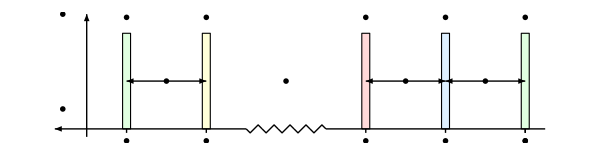

```mathematica
p1=Module[{
L=5,
tmin=-1.5,
tdash=0.75,
dt={1,0},
pulsew=0.1,
pulseh=1.2,
hoff=0.3,
voff=0.2,
eps=0.1,
op=Magnification->1.5,
p0,pt,v,p,tick,zigzag,pulse,twoarrows},

p0={0,0};
pt={-L,0};

pulse[x_,label_,color_,edge_:Black]:=
{
EdgeForm[edge],FaceForm[color],
Rectangle[{x-pulsew/2,0},{x+pulsew/2,pulseh}],
Text[MaTeX[label,op],{x,pulseh+voff}]
};

tick[x_,label_,h_:0.05]:={
Line[{{x,-h},{x,h}}],
Text[MaTeX[label,op],{x,-h-2h}]
};

zigzag[x1_,x2_,n_,amp_]:=Module[{dx=(x2-x1)/(4n)},
Table[Line[{{x1+i*4dx,0},{x1+i*4dx+dx,amp},{x1+i*4dx+2dx,0},{x1+i*4dx+3dx,-amp},{x1+(i+1)*4dx,0}}],{i,0,n-1}]];

twoarrows[x1_,x2_,label_]:={
Arrowheads[{-0.02,0.02}],Arrow[{{x1,pulseh/2},{x2,pulseh/2}}],
Text[MaTeX[label,op],{(x1+x2)/2,pulseh/2},Background->White]
};

Graphics[{
tick[0,"t_0"],
tick[-1,"t_1"],pulse[-1,"P_1",LightBlue],
tick[-2,"t_2"],pulse[-2,"P_2",LightRed],
tick[-4,"t_{L-1}"],pulse[-4,"P_{L-1}",LightYellow],
tick[-5,"t_{L}"],pulse[-5,"P_{L}",LightGreen],

tick[0,""],pulse[0,"P'_{L}",LightGreen,Dashed],

twoarrows[0,-1,"\\tau_1"],
twoarrows[-2,-1,"\\tau_2"],
twoarrows[-5,-4,"\\tau_L"],
Text[MaTeX["\\cdots",op],{-3,0.5 pulseh}],

Arrowheads[0.025],
Line[{{0.25,0},{-2.5,0}}],
zigzag[-2.5,-3.5,5,0.05],
Arrow[{{-3.5,0},{-5.9,0}}],
Arrow[{{-5.5,-0.1},{-5.5,1.2pulseh}}],
Text[MaTeX["H_{\\mathrm{ctrl}}",op],{-5.8,1.2pulseh}],
Text[MaTeX["t",op],{-5.8,0.25}]
},ImageSize->600]

]
```

```mathematica
Export[NotebookDirectory[]<>"pulse.pdf",p1]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/pulse.pdf

```mathematica
300*150
```

45000

```mathematica
colors={Green,Yellow,Red,Blue};
```

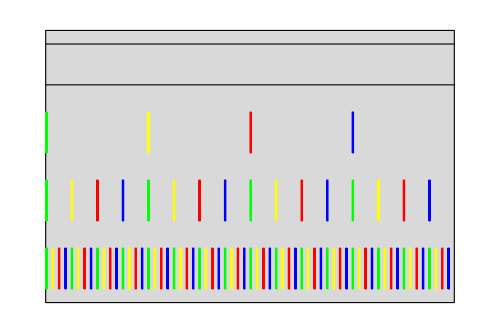

```mathematica
Module[{L=6, h=-1,hp=0.2,level=4},
Graphics[{
EdgeForm[Black],FaceForm[LightGray],Rectangle[{0,0},{L,-level}],
FaceForm[LightGray],Rectangle[{0,-hp},{L ,h+hp}],
Table[{EdgeForm[colors[[Mod[m,4]+1]]],FaceForm[colors[[Mod[m,4]+1]]],Rectangle[{L (m/4^n),n h- hp},{L (m/4^n)+0.02,(n+1)h+hp}]},{n,1,level-1},{m,0,4^n-1}]
},ImageSize->500]
]
```

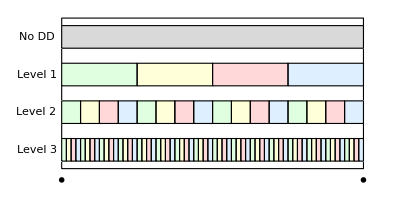

```mathematica
p2=Module[{L=8, h=-1,hp=0.2,level=3,colors},
colors={LightGreen,LightYellow,LightRed,LightBlue};
Graphics[{
EdgeForm[Black],FaceForm[White],Rectangle[{0,0},{L,-level-1}],
FaceForm[LightGray],Rectangle[{0,-hp},{L ,h+hp}],
Table[{FaceForm[colors[[Mod[m,4]+1]]],Rectangle[{L (m/4^n),n h- hp},{L ((m+1)/4^n),(n+1)h+hp}]},{n,1,level},{m,0,4^n-1}],
Text["No DD",{-1/12L,(1/2) h}],
Table[Text["Level "<>ToString[n],{-1/12L,(n+1/2) h}],{n,1,level}],
Text[MaTeX["0",Magnification->1.25],{0,4.3 h}],Text[MaTeX["T",Magnification->1.25],{L,4.3 h}]
}]
]
```

```mathematica
a=1;
```

```mathematica
"pp"<>ToString[a]
```

pp1

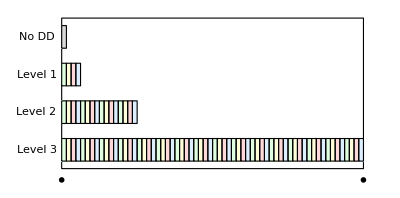

```mathematica
p3=Module[{L=8, h=-1,hp=0.2,level=3,dL,colors},
colors={LightGreen,LightYellow,LightRed,LightBlue};
dL=L/4^level;
Graphics[{
EdgeForm[Black],FaceForm[White],Rectangle[{0,0},{L,-level-1}],
FaceForm[LightGray],Rectangle[{0,-hp},{dL ,h+hp}],
Table[{FaceForm[colors[[Mod[m,4]+1]]],Rectangle[{m dL,n h- hp},{(m+1)dL,(n+1)h+hp}]},{n,1,level},{m,0,4^n-1}],
Text["No DD",{-1/12L,(1/2) h}],
Table[Text["Level "<>ToString[n],{-1/12L,(n+1/2) h}],{n,1,level}],
Text[MaTeX["0",Magnification->1.25],{0,4.3 h}],Text[MaTeX["4^n \\tau",Magnification->1.25],{L,4.3 h}]
}]
]
```

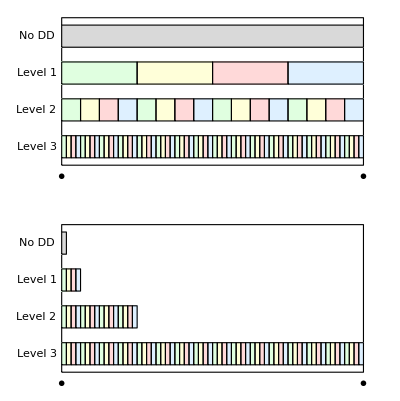

```mathematica
p23=GraphicsColumn[{p2,p3}]
```

```mathematica
Export[NotebookDirectory[]<>"memory-vs-computation.pdf",p23]
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/memory-vs-computation.pdf

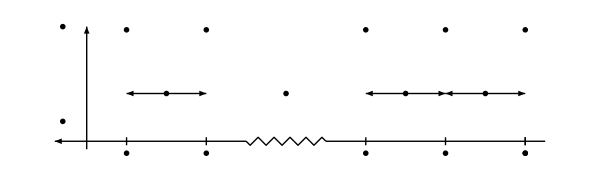
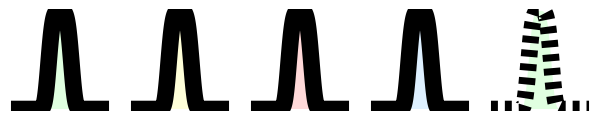

```mathematica
p4=Module[{
L=5,
tmin=-1.5,
tdash=0.75,
dt={1,0},
pulsew=0.2,
pulseh=1.2,
hoff=0.3,
voff=0.2,
eps=0.1,
op=Magnification->1.5,
p0,pt,v,p,tick,zigzag,pulse,twoarrows},

p0={0,0};
pt={-L,0};

tick[x_,label_,h_:0.05]:={
Line[{{x,-h},{x,h}}],
Text[MaTeX[label,op],{x,-h-2h}]
};

zigzag[x1_,x2_,n_,amp_]:=Module[{dx=(x2-x1)/(4n)},
Table[Line[{{x1+i*4dx,0},{x1+i*4dx+dx,amp},{x1+i*4dx+2dx,0},{x1+i*4dx+3dx,-amp},{x1+(i+1)*4dx,0}}],{i,0,n-1}]];

twoarrows[x1_,x2_,label_]:={
Arrowheads[{-0.02,0.02}],Arrow[{{x1,pulseh/2},{x2,pulseh/2}}],
Text[MaTeX[label,op],{(x1+x2)/2,pulseh/2},Background->White]
};

pulse[x_,label_,color_,edge_:Black]:=
{
Text[MaTeX[label,op],{x,pulseh+voff}],
Inset[Plot[E^(-t^4),{t,-4,4},Axes->None,PlotRange->{0,1},Filling->Axis,
AspectRatio->pulseh/(2pulsew),PlotStyle->Directive[edge,Thickness[Scaled[0.03]]],FillingStyle->color
],{x,0},{0,0},{Automatic,pulseh}]
};

Graphics[{
tick[0,"t_0"],
tick[-1,"t_1"],pulse[-1,"P_1",LightBlue],
tick[-2,"t_2"],pulse[-2,"P_2",LightRed],
tick[-4,"t_{L-1}"],pulse[-4,"P_{L-1}",LightYellow],
tick[-5,"t_{L}"],pulse[-5,"P_{L}",LightGreen],

tick[0,""],pulse[0,"P'_{L}",LightGreen,{Dashed,Black}],

twoarrows[0,-1,"\\tau_1"],
twoarrows[-2,-1,"\\tau_2"],
twoarrows[-5,-4,"\\tau_L"],
Text[MaTeX["\\cdots",op],{-3,0.5 pulseh}],
Arrowheads[0.025],
Line[{{0.25,0},{-2.5,0}}],
zigzag[-2.5,-3.5,5,0.05],
Arrow[{{-3.5,0},{-5.9,0}}],
Arrow[{{-5.5,-0.1},{-5.5,1.2pulseh}}],
Text[MaTeX["H_{\\mathrm{ctrl}}",op],{-5.8,1.2pulseh}],
Text[MaTeX["t",op],{-5.8,0.25}]
},ImageSize->600,PlotRange->{Automatic,{-1.2hoff,pulseh+1.2hoff}}]

]
```

```mathematica
Export[NotebookDirectory[]<>"pulse.pdf",p4]
"/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/pulse.pdf"
```

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/pulse.pdf

/Users/jiaan/Desktop/DD-threshold/dd-efficacy/img/pulse.pdf

```mathematica
E^(-x^4)==0.1
```